## Euler’s Method

Check work from MATLAB and Python.

```mathematica
Clear["Global`*"]
```

## Check 1:

From Computational Quantum Mechanics page 190

```mathematica
ode = y'[x] == x y[x];
```

```mathematica
initConds = y[0] == 2;
```

```mathematica
a = 0; b = 1;
```

```mathematica
sAuto = NDSolve[{ode, initConds}, y, {x, a, b}]
```

{{y→InterpolatingFunction[…]}}

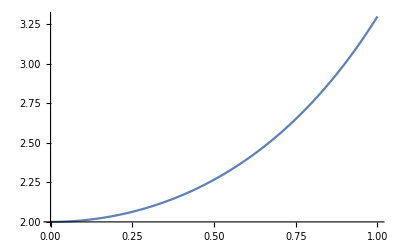

```mathematica
plotAutoMethod = Plot[Evaluate[y[x]/.sAuto], {x, a, b}, PlotRange->All]
```

```mathematica
sEuler = NDSolve[{ode, initConds}, y, {x, a, b}, Method->"ExplicitEuler"]
```

{{y→InterpolatingFunction[{{0., 1.}}, <>]}}

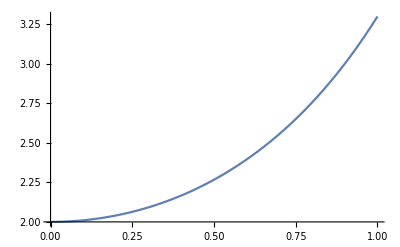

```mathematica
plotEulerMethod = Plot[Evaluate[y[x]/.sEuler], {x, a, b}, PlotRange->All]
```

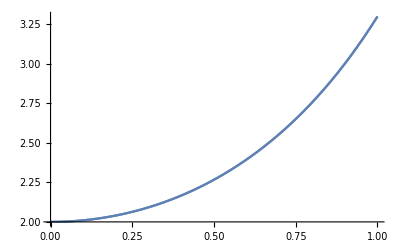

```mathematica
Show[{plotAutoMethod, plotEulerMethod}]
```

#### Table data:

```mathematica
Table[{x, y[x]/.sEuler}, {x, a, b, 0.01}]
```

{{0.,{2.}},{0.01,{2.0001}},{0.02,{2.0004}},{0.03,{2.0009}},{0.04,{2.0016}},{0.05,{2.0025}},{0.06,{2.0036}},{0.07,{2.0049}},{0.08,{2.00641}},{0.09,{2.00812}},{0.1,{2.01002}},{0.11,{2.01214}},{0.12,{2.01445}},{0.13,{2.01697}},{0.14,{2.01969}},{0.15,{2.02262}},{0.16,{2.02576}},{0.17,{2.02911}},{0.18,{2.03266}},{0.19,{2.03642}},{0.2,{2.0404}},{0.21,{2.04459}},{0.22,{2.04899}},{0.23,{2.0536}},{0.24,{2.05843}},{0.25,{2.06348}},{0.26,{2.06875}},{0.27,{2.07424}},{0.28,{2.07995}},{0.29,{2.08589}},{0.3,{2.09205}},{0.31,{2.09844}},{0.32,{2.10506}},{0.33,{2.11191}},{0.34,{2.119}},{0.35,{2.12632}},{0.36,{2.13389}},{0.37,{2.14169}},{0.38,{2.14973}},{0.39,{2.15803}},{0.4,{2.16657}},{0.41,{2.17536}},{0.42,{2.18441}},{0.43,{2.19371}},{0.44,{2.20327}},{0.45,{2.2131}},{0.46,{2.22319}},{0.47,{2.23355}},{0.48,{2.24419}},{0.49,{2.2551}},{0.5,{2.26629}},{0.51,{2.27776}},{0.52,{2.28952}},{0.53,{2.30157}},{0.54,{2.31392}},{0.55,{2.32656}},{0.56,{2.33951}},{0.57,{2.35277}},{0.58,{2.36634}},{0.59,{2.38022}},{0.6,{2.39442}},{0.61,{2.40895}},{0.62,{2.42381}},{0.63,{2.43901}},{0.64,{2.45455}},{0.65,{2.47043}},{0.66,{2.48666}},{0.67,{2.50325}},{0.68,{2.52021}},{0.69,{2.53753}},{0.7,{2.55523}},{0.71,{2.5733}},{0.72,{2.59177}},{0.73,{2.61063}},{0.74,{2.62989}},{0.75,{2.64955}},{0.76,{2.66963}},{0.77,{2.69013}},{0.78,{2.71106}},{0.79,{2.73243}},{0.8,{2.75424}},{0.81,{2.7765}},{0.82,{2.79922}},{0.83,{2.82241}},{0.84,{2.84607}},{0.85,{2.87022}},{0.86,{2.89487}},{0.87,{2.92002}},{0.88,{2.94568}},{0.89,{2.97186}},{0.9,{2.99858}},{0.91,{3.02584}},{0.92,{3.05365}},{0.93,{3.08203}},{0.94,{3.11098}},{0.95,{3.14052}},{0.96,{3.17065}},{0.97,{3.2014}},{0.98,{3.23276}},{0.99,{3.26476}},{1.,{3.29741}}}